# Losses in HCF

```mathematica
Clear["Global`*"]
```

## MARCATILI and SCHMELTZER

### Glass

```mathematica
nExt=1.5;(*external refective index, glass*)
nInt=1;(*internal refractive index, n_air = 1*)
ν=nExt/nInt;(*complex refractive index of external material*)
νn=(1/2(ν^2+1))/(√(ν^2-1));(*for HEnm modes*)
(*1/(√(ν^2-1));*)(*for TE0m modes*)
(*ν^2/(√(ν^2-1));*)(*for TM0m modes*)
unm=BesselJZero[0,1];
(*a is inner radius of fiber*)
(*λ is wavenlength of laser in m*)
α[λ_,LA_]=(unm/(2π))^2 LA^3/λ Re[νn];(*LA = λ/a fro plotting purposes*)
(*LogLogPlot[8686*{α[10^-4,LA],α[10^-5,LA],α[10^-6,LA],α[10^-7,LA]},{LA,.05,.0001},PlotRange->{.01,50},Frame->True]*)
α[10^-6,10^-6/10^-3]*8686
Exp[-α[10^-6,10^-6/10^-3]*100]
```

1.84938

0.978934

### Aluminum

```mathematica
nExt=1.4358+ⅈ*9.4953;(*external refective index*)
nInt=1;(*internal refractive index, n_air = 1*)
ν=nExt/nInt;(*complex refractive index of external material*)
νn=1/(√(ν^2-1));(*for TE0m modes*)
unm=BesselJZero[-1,1];
a=10^-3;(*inner radius of fiber*)
λ=10^-6;(*wavenlength of laser in m*)
α=(unm/(2π))^2 λ^2/a^3 Re[νn];
8686*α
```

0.0495088

```mathematica
Clear["Global`*"]
```

## Nubling & Harrington

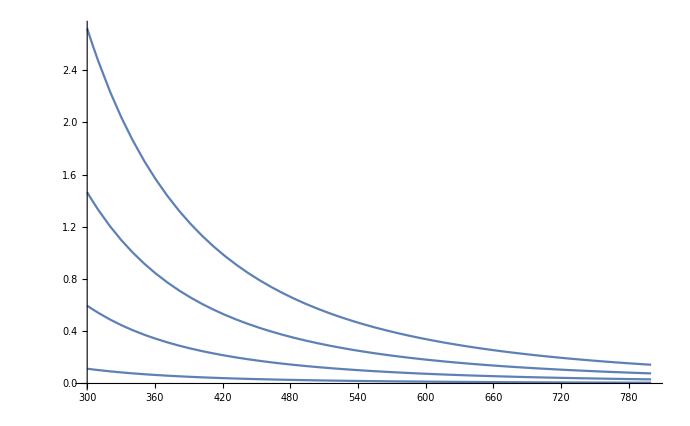

```mathematica
n=0.020000;(*real part of refective index of metal guide*)
k=7.1155;(*imaginary part of refractive index of metal guide, n_air = 1*)
nd=2.22;(*AgI, https://www.matweb.com/search/datasheet_print.aspx?matguid=024bcb4f2a0140aeb1720df8e4982942&n=1*)
λ=1*10^-6;(*wavenlength of laser in m*)
α[unm_,a_]=(unm/(2π))^2 λ^2/a^3 n/(n^2+k^2)1/2(1+nd^2/(√(nd^2-1)))^2;
Plot[8686*{α[BesselJZero[0,1],r*10^-6],α[BesselJZero[0,2],r*10^-6],α[BesselJZero[0,3],r*10^-6],α[BesselJZero[0,4],r*10^-6]},{r,300,800},PlotRange->All]
```

```mathematica
Clear["Global`*"]
```

## PBPL Fiber

```mathematica
(* nExt=0.19300+ⅈ*1.8450 external refective index, glass*)
(*nInt=1 internal refractive index, n_air = 1*)
(*ν=nExt/nInt complex refractive index of external material*)
(*https://refractiveindex.info/?shelf=main&book=Ag&page=Ciesielski*)
νn[ν_]=(1/2(ν^2+1))/(√(ν^2-1));(*for HEnm modes*)
(*a is inner radius of fiber*)
(*λ is wavenlength of laser in m*)
α[unm_,λ_,a_,ν_]=(unm/(2π))^2 λ^2/a^3 Re[νn[ν]];(*in Np/m*)
αdB[unm_,λ_,a_,ν_]=α[unm,λ,a,ν]*8.686;(*in dB/m*)
Exp[-α[BesselJZero[0,1],800*10^-9,100*10^-6,0.093994+ⅈ*5.2123]*.3]
Exp[-α[BesselJZero[0,1],400*10^-9,100*10^-6,0.19300+ⅈ*1.8450]*.3]
Exp[-α[BesselJZero[0,1],266*10^-9,100*10^-6,1.3905+ⅈ*1.2542]*.3]
```

0.998611

0.999133

0.997073

```mathematica
αdB[BesselJZero[0,1],800*10^-9,500*10^-6,0.093994+ⅈ*5.2123]
αdB[BesselJZero[0,1],400*10^-9,500*10^-6,0.19300+ⅈ*1.8450]
αdB[BesselJZero[0,1],266*10^-9,500*10^-6,1.3905+ⅈ*1.2542]
```

0.000322035

0.000200829

0.000678988

```mathematica
Clear["Global`*"]
```

## Overlap Integral

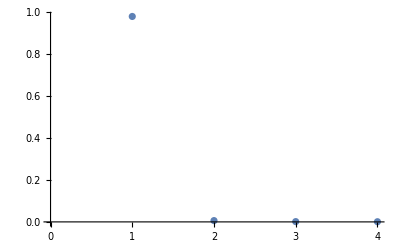

0.980713

0.00618262

```mathematica
a=100*10^-6;
n[w_,m_]:=((NIntegrate[Exp[-r^2/w^2]BesselJ[0,BesselJZero[0,m]*r/a]*r,{r,0,a}])^2)/(NIntegrate[Exp[-2 R^2]*R*w^2,{R,0,Infinity}]*NIntegrate[(BesselJ[0,BesselJZero[0,m]*r/a])^2*r,{r,0,a}]);
ListPlot[{n[.64*a,1],n[.64*a,2],n[.64*a,3],n[.64*a,4]}]
n[.64*a,1]
n[.64*a,2]
(*Plot[n[WA*a,1],{WA,.1,1}]*)
```